# MA2330

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``row)_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```

## Chapter 1 : Linear Equations in Linear Algebra

### 1.1 Systems of Linear Equations.

#### Small Example

A linear system looks like this 
	4 x_1 | + | 3 x_2 | - | x_3 | = | 1
-2 x_1 | + | x_2 |   |   | = | 2
0.5 x_1 |   |   | + | X_3 | = | -2
It will not always be lined up as neatly!

The variables are x_1,x_2, and x_3.

Not all variables in the real world are called x_i

The coefficient matrix is A=(4 | 3 | -1
-2 | 1 | 0
0.5 | 0 | 1)

The coefficients of the first equation are 4,3,-1 etc.

Coefficients in most real world problems are real numbers (which our book writes as ℝ)

Most of our hand examples will have integers!

The right hand side (RHS) vector is b=(1
2
-2)

In fancy terminology we have ∑_(j=1)^3 a_(i,j)x_j=b_i  for i=1,2, and 3 which we are going to learn to write as A x = b

For i=1 we have a_(1,1)x_1+a_(1,2)x_2+a_(1,3)x_3=b_1

The matrix A∈ℝ^(3 × 3), the RHS b∈ℝ^3, and our task would be to compute x∈ℝ^3.

To save ourselves from copying variables the first thing we will always do is write down the matrix.

We will almost always call our variables x and our matrices A. When we are solving A x=b we will write down the augmented matrix by sticking the right hand side b on the back of A. The augmented matrix is written (A | | | b)

In this example (A | | | b)=(4 | 3 | -1 | 1
-2 | 1 | 0 | 2
0.5 | 0 | 1 | -2)∈ℝ^(3 × 4)

You get the matrix by lining up the terms carefully and then you neglect to write down the variables.

#### Nonlinear Terms

Any term involving the product of variables or any non-trivial function (Sine, Cosine, Log, Exp, ...) is nonlinear.   For example, x_1 x_2 is non-linear as is sin(x_3).

All the terms in all our equations need to be linear it is in the course name!

#### Geometry

Any linear equation in ℝ^2 defines a line. A set of two linear equations defines two lines in ℝ^2.

Nonparallel lines intersect in a single point.

Parallel lines never intersect.

Unless they lie right on top of each other.

Nearly parallel lines intersect but the intersection point is twitchy.

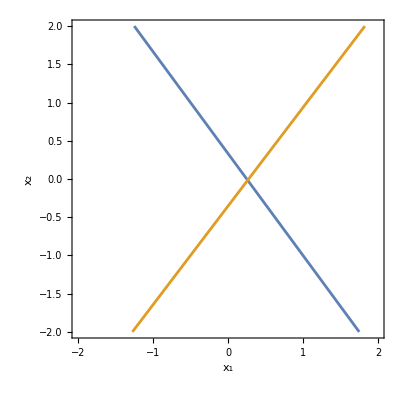

```mathematica
a1={4,3};b1=1;
a2={4,-3.1};b2 =1.1;
ContourPlot[ {
a1.{x1,x2}==b1,
a2.{x1,x2}==b2
},
{x1,-2,2},{x2,-2,2},
AxesLabel->{"x_1","x_2"}]
```

Any linear equation in ℝ^3 defines a plane. A set of three linear equations defines three planes in ℝ^3

Three planes usually intersect in a single point.

Some degenerate sets of planes can fail to intersect.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3={0.5,0,1};b3=-2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-2,2},{x2,-2,2},{x3,-2,2},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

Here is a degenerate set of planes.  We made a degenerate set by adding a_1 to a_2 to define a_3.  This set of three equations has no solution!

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3=a1+a2;b3=-2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-12,12},{x2,-12,12},{x3,-12,12},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

Here is a degenerate set of planes with lots of solutions.  This degenerate set adds a_1 to a_2 to define a_3 and b_1 to b_2 to get b_3.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3=a1+a2;b3=b1+b2;
ContourPlot3D[ {
a1.{x1,x2,x3}==b1,
a2.{x1,x2,x3}==b2,
a3.{x1,x2,x3}==b3
},
{x1,-12,12},{x2,-12,12},{x3,-12,12},
AxesLabel->{"x_1","x_2","x_3"}]
```

-Graphics3D-

#### Solving Equations by Hand

To solve a set of linear equations you simply eliminate variables by artfully combing equations.  It is good to be organized when you do this to avoid going in circles. We are going to do this on the board with the variables and show the matching operations on the augmented matrix

The operations on the augmented matrix are three types of elementary row operations

Replace one row by the sum of itself and a multiple of another row.

Interchange two rows.

Scale all entries in a row by a non-zero constant.

#### Solving Equations by Computer: Small Systems

All technical computational tools can solve linear systems.

```mathematica
a1={4,3,-1};b1=1;
a2={-2,1,0};b2 =2;
a3={0.5,0,1};b3=-2;
Solve[ 
{a1.{x1,x2,x3}==b1,a2.{x1,x2,x3}==b2,a3.{x1,x2,x3}==b3},
{x1,x2,x3}]
```

{{x1→-0.666667,x2→0.666667,x3→-1.66667}}

The matrix form is simpler.

```mathematica
A={
{4,3,-1},
{-2,1,0},
{0.5,0,1}};b={1,2,-2};
LinearSolve[A,b]
```

{-0.666667,0.666667,-1.66667}

There is a RowReduce command that mimics what we do by hand.

```mathematica
AugAb={{4,3,-1,1},{-2,1,0,2},{0.5,0,1,-2}};
RRef=RowReduce[AugAb];
MatrixForm[RRef]
```

(1 | 0. | 0. | -0.666667
0 | 1 | 0. | 0.666667
0 | 0 | 1 | -1.66667)

You can build the augmented matrix from A and b.

```mathematica
ArrayFlatten[{{A,{b}ᵀ}}]
```

{{4,3,-1,1},{-2,1,0,2},{0.5,0,1,-2}}

XYZ Here

#### Definitions, Questions, and Answers

Definition
Matrices are row equivalent if you can go from one to the other using Elementary Row Ops.

Statement
Systems with row equivalent Augmented Matrices have the same solutions.

Question
Does a system have a solution? In other words does a solution exist?

Question
If a solution exists, is it the only one? In other words, is the solution unique?

#### Solving Equations by Computer: Larger Systems

The computer organizes the computation and can do much larger computations. Lets see what big is? Our only real problem is making big matrices: we do not want to type them.

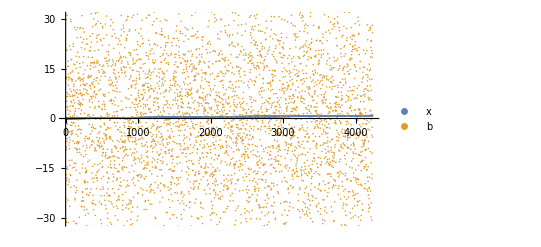

```mathematica
n=4234;
xIn=Table[ Sin[x],{x,0.0,1,1/n}];
A=RandomReal[{-1,1},{n+1,n+1}];
b=A.xIn;
Map[Dimensions,{A,xIn,b}] ;
ListPlot[{xIn,b},PlotLegends->{"x","b"}]
```

{0.5,Null}

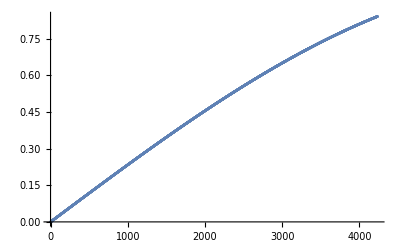

```mathematica
Timing[xOut=LinearSolve[A,b];]

ListPlot[xOut]
```

A good question is what will break first if we try to do larger computations?

#### Solving Equations by Computer: Real Matrices

What do real matrices look like.  A National Institute of Science and Technology (NIST) web page  https://math.nist.gov/MatrixMarket/ has a collection of real matrices.   Here is one

SparseArray[…]

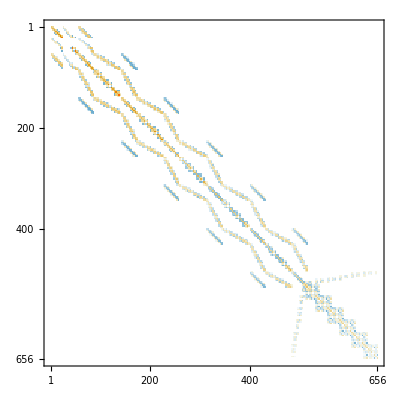

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/fidap/fidap021.mtx.gz"]
MatrixPlot[A]
```

Here is a larger matrix used in a LinearSolve.

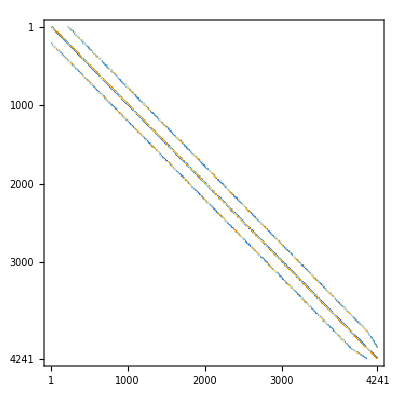

{0.03125,Null}

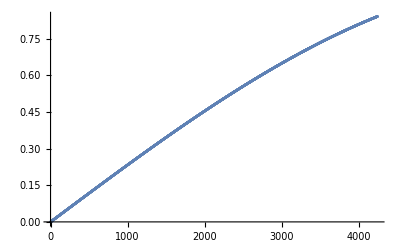

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/drivcav/e20r5000.mtx.gz"];
MatrixPlot[A]
n=Length[A];xIn=Table[ Sin[x],{x,0.0,1,1/(n-1)}];b=A.xIn;
Timing[xOut=LinearSolve[A,b];]
ListPlot[xOut]
```

#### Computational Examples

Ex2 (text)
2 | x_1 | + | -2 | x_2 | + | 1 | x_3 | = | 0
0 | x_1 | + | 2 | x_2 | + | -8 | x_3 | = | 8
5 | x_1 | + | 0 | x_2 | + | -5 | x_3 | = | 10→(1 | -2 | 1 | 0
0 | 2 | -8 | 8
5 | 0 | -5 | 10)~(1 | -2 | 1 | 0
0 | 1 | -4 | 4
0 | 0 | 1 | -1)→x_1 | = | 0-1 x_3+2 x_2
x_2 | = | 4+4 x_3
x_3 | = | -1

Ex3 (text)
0 | x_1 | + | 1 | x_2 | + | -4 | x_3 | = | 8
2 | x_1 | + | -3 | x_2 | + | 2 | x_3 | = | 1
4 | x_1 | + | -8 | x_2 | + | 12 | x_3 | = | 1→(0 | 1 | -4 | 8
2 | -3 | 2 | 1
4 | -8 | 12 | 1)~(2 | -3 | 2 | 1
0 | 1 | -4 | 8
0 | 0 | 0 | 15)→2 x_1 | = | 1-2 x_3+3 x_2
x_2 | = | 8+4 x_3
x_3 | = | !!!
There is no such x_3.  So there is no solution to the original system.

Suppose you had the same matrix but a different right hand side and you got
0 | x_1 | + | 1 | x_2 | + | -4 | x_3 | = | 8
2 | x_1 | + | -3 | x_2 | + | 2 | x_3 | = | 1
4 | x_1 | + | -8 | x_2 | + | 12 | x_3 | = | ?→(0 | 1 | -4 | 8
2 | -3 | 2 | 1
4 | -8 | 12 | ?)~(2 | -3 | 2 | 1
0 | 1 | -4 | 8
0 | 0 | 0 | 0)→2 x_1 | = | 1-2 x_3+3 x_2
x_2 | = | 8+4 x_3
0 x_3 | = | 0
Any x_3 works! So there are lots of solutions!!

#### Systems of Linear Equations: Skills and Terminology

Linear System ⟷ Augmented Matrix

Row Reduction to Echelon Form (RREF) using Row Operations (RO)

Interpretation of RREF Matrix

Existence and uniqueness of solutions of A x= b from RREF

### 1.2 Row Reduction and Echelon Form

#### Definitions and Terminology

The leading entry in a row is the left most non-zero in the row.  The locations of a leading entry is a pivot position

Row Echelon Form conditions 1, 2, and 3.  Reduced Row Echelon Form conditions 1, 2, 3, 4, and 5.

All Non-zero rows are above zero rows.

Leading entry of a row is to the right of the leading entry above.

Entries below a leading entry are zero.

Leading entries are 1.

The leading 1 is the only non-zero entry in its column.

Theorem 1: A matrix A is row equivalent to exactly one RREF

#### Algorithm for RREF

Start with the left hand column and work to the right.

Select a non-zero entry in this column as pivot. Interchange row 1 and the selected row to move the pivot into the pivot position.

Zero all the entries below the pivot using ROs.

Repeat this process on the submatrix below and to the right of the pivot position.

Start with the rightmost pivot and work to the left. Scale the pivot to 1 with an RO and zero all the entries above the pivot with ROs.

The forward phase 1-4 generates a REF. Step 5 takes you all the way to the unique RREF.

Computers usually switch the largest entry in a column to the pivot position.  This partial pivoting reduces roundoff errors in the computation.

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``row)_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```

```mathematica
AAug=REF={
{0,3,-6,6,4,-5},
{3,-7,8,-5,8,9},
{3,-9,12,-9,6,15},
{3,-9,1,-9,6,15}
};
REF=RowSwitch[REF,{1,3}];
REF=RowAdd[REF,{{{2,-1},{4,-1}},1}];
REF=RowAdd[REF,{{{3,-3/2}},2}];
REF=RowSwitch[REF,{3,4}];
REF=RowAdd[REF,{{{2,-2},{1,-6}},4}];
REF=RowScale[REF,{3,-1/11}];
REF=RowAdd[REF,{{{2,4},{1,-12}},3}];
REF=RowScale[REF,{2,1/2}];
REF=RowAdd[REF,{{{1,9}},2}];
REF=RowScale[REF,{1,1/3}];
```

(3 | -9 | 12 | -9 | 6 | 15
3 | -7 | 8 | -5 | 8 | 9
0 | 3 | -6 | 6 | 4 | -5
3 | -9 | 1 | -9 | 6 | 15)row_(RowBox[{)→row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→row_(RowBox[{)
row_(RowBox[{)

(3 | -9 | 12 | -9 | 6 | 15
0 | 2 | -4 | 4 | 2 | -6
0 | 3 | -6 | 6 | 4 | -5
0 | 0 | -11 | 0 | 0 | 0)row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))

(3 | -9 | 12 | -9 | 6 | 15
0 | 2 | -4 | 4 | 2 | -6
0 | 0 | 0 | 0 | 1 | 4
0 | 0 | -11 | 0 | 0 | 0)row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)

(3 | -9 | 12 | -9 | 6 | 15
0 | 2 | -4 | 4 | 2 | -6
0 | 0 | -11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→row_(RowBox[{)
row_(RowBox[{)→row_(RowBox[{)

(3 | -9 | 12 | -9 | 0 | -9
0 | 2 | -4 | 4 | 0 | -14
0 | 0 | -11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)
row_(RowBox[{)

(3 | -9 | 12 | -9 | 0 | -9
0 | 2 | -4 | 4 | 0 | -14
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)→(RowBox[{)_(RowBox[{)
row_(RowBox[{)

(3 | -9 | 0 | -9 | 0 | -9
0 | 2 | 0 | 4 | 0 | -14
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)
row_(RowBox[{)

(3 | -9 | 0 | -9 | 0 | -9
0 | 1 | 0 | 2 | 0 | -7
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)
row_(RowBox[{)→(FractionBox[)_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)

(3 | 0 | 0 | 9 | 0 | -72
0 | 1 | 0 | 2 | 0 | -7
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)→ row_(RowBox[{)+((RowBox[{)_(RowBox[{))
row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)

(1 | 0 | 0 | 3 | 0 | -24
0 | 1 | 0 | 2 | 0 | -7
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)row_(RowBox[{)→(FractionBox[)_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)
row_(RowBox[{)

We can check the answer! Uniqueness says they need to match!

```mathematica
RowReduce[AAug]//MatrixForm
```

(1 | 0 | 0 | 3 | 0 | -24
0 | 1 | 0 | 2 | 0 | -7
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 4)

#### Solutions of Linear Equations

Our example matrix is the augmented matrix for the linear system
	A x = b
of three equations in 5 unknowns (x_1,x_2,x_3,x_4, and x_5) where 
	A=(0 | 3 | -6 | 6 | 4
3 | -7 | 8 | -5 | 8
3 | -9 | 12 | -9 | 6)  and b=(-5
9
15)
Since row reduction does not change the solution set the solutions are the same as those of the system with the simpler augmented matrix 
	(1 | 0 | -2 | 3 | 0 | -24
0 | 1 | -2 | 2 | 0 | -7
0 | 0 | 0 | 0 | 1 | 4)
which comes from the simpler system
	 x_1-2 x_3+3 x_4 | = | -24
x_2-2 x_3+2 x_4 | = | -7
x_5 | = | 4
This is the same as 
	x_1 | = | -24 | + | 2  | x_3 | + | -3 | x_4
x_2 | = | -7 | + | 2 | x_3 | + | -2 | x_4
x_5 | = | 4 |   |   |   |   |   |  
The variables x_1,x_2,and x_5 are called basic. The variables x_3 and x_4 are called free.

We can write all the solutions as
	x=(x_1
x_2
x_3
x_4
x_5)=(-24
-7
0
0
4)+x_3(2
2
1
0
0)+x_4(-3
-2
0
1
0)

#### More solutions of Linear Equations

Example A. Suppose the RREF of the augmented matrix for a system is
	(1 | 2 | 0 | 2
0 | 0 | 1 | 3)
Then the solution set of the original system is
	x=(x_1
x_2
x_3)=(2
0
3)+x_2(-2
1
0)

Example B. Suppose the RREF of the augmented matrix for a linear system is
	(1 | 2 | 0 | 2
0 | 0 | 0 | 3)
Then the solution set of the original system is the same as the solution set of 
	x_1=2-2 x_2 and 0 x_3=3.
There are no solutions of this simple system.  The original system has no solutions.

Example C. Suppose the RREF of the augmented matrix for a linear system is
	(1 | 2 | 0 | 0 | 3
0 | 0 | 1 | 0 | 5
0 | 0 | 0 | 1 | 7)
Then the solution set is 
	x=(x_1
x_2
x_3
x_4)=(3
0
5
7)+x_2(-2
1
0
0)

Example D. Suppose the RREF of the augmented matrix for a linear system is
	(1 | 0 | 2 | 0 | 6
0 | 1 | 8 | 0 | 3
0 | 0 | 0 | 1 | 9)
Then the solution set is 
	x=(x_1
x_2
x_3
x_4)=(6
3
0
9)+x_3(-2
-8
1
0)

Example E. Suppose the RREF of the augmented matrix for a linear system is
	(1 | 0 | 2 | 0 | 6
0 | 1 | 8 | 0 | 3
0 | 0 | 0 | 1 | 9
0 | 0 | 0 | 0 | 6)
No solution!

Example F. Suppose the RREF of the augmented matrix for a linear system is
	(1 | 0 | 0 | 0 | 6
0 | 1 | 0 | 0 | 3
0 | 0 | 1 | 0 | 9
0 | 0 | 0 | 1 | 6)
One unique solution! 
x=(x_1
x_2
x_3
x_4)=(6
3
9
6)

### 1.3 Vector Equations.

An n vector is an ordered list of n numbers: a one-column skinny matrix.  Books and computer programs use all sorts of notation for vectors.  Our book uses square brackets.  Other books use round parenthesis.  Mathematica uses curly braces. We are not picky about brackets but computer programs are picky.

ℝ^n means (x_1
⋮
x_n)  with component x_i satisfying -∞<x_i<∞. ℂ^n means (z_1
⋮
z_n) with complex component z_i.

Add vectors by adding matching components.  Scalar multiplication by α∈ℝ is pretty simple 
	u+v=(u_1+v_1
⋮
u_n+v_n)   and α u=(α u_1
⋮
α u_n) 
and not surprisingly 	
	u+v=u+v |   | α (u+v)=α u+α v
(u+v)+w=u+(v+w) |   | u (α+β)=α u+β u
u+0=u |   | α (β u)=β (α u)
u-u=0 |   | 1 u=u   
Yes our book puts them in a box!

#### Linear Combinations

A linear combination of v_1,v_2,…,v_p in ℝ^n with scalar weights c_1,c_2,…,c_p is the vector
	y=c_1 v_1+c_2 v_2+…+c_p v_p=∑_(i=1)^p c_i v_i
The span of v_1,v_2,…,v_p in ℝ^n is the set of all linear combinations. In symbols
	span(v_1,v_2,…,v_p)={c_1 v_1+c_2 v_2+…+c_p v_p with -∞<c_i<∞}.

The span of the two vectors a_1={1,2,3} and a_2={-2,1,4} is the plane in ℝ^3 pictured below.

```mathematica
a1={7,6,4}; a2={-7,-6,3.2};
Show[
ParametricPlot3D[c1 a1+ c2 a2,{c1, -2,2},{c2,-2,2}],
Graphics3D[{Thick,
{Red, Arrow[{{0,0,0},a1}]},
{Blue, Arrow[{{0,0,0},a2}]}}]]
```

-Graphics3D-

```mathematica
a1={10,2,3}; a2={-2,1,5};
Show[
ParametricPlot3D[c1 a1+ c2 a2,{c1, -2,2},{c2,-2,2}],
Graphics3D[{Thick,
{Red, Arrow[{{0,0,0},a1}]},
{Blue, Arrow[{{0,0,0},a2}]}}]]
```

-Graphics3D-

```mathematica
a1={1,2,3}; a2=2a1;
Show[
ParametricPlot3D[c1 a1+ c2 a2,{c1, -2,2},{c2,-2,2}],
Graphics3D[{Thick,
{Red, Arrow[{{0,0,0},a1}]},
{Blue, Arrow[{{0,0,0},a2}]}}]]
```

-Graphics3D-

We want to see if a vector b∈ℝ^n is in the span(a_1,a_2,…,a_m).

By definition b is in span(a_1,a_2) iff there are scalars x_1 and x_2 satisfying
	a_1 x_1+a_2 x_2=b.
For the example if a_1=(1
2
3) and a_2=(-2
1
4)  our equation is 
	(1
2
3)x_1+(-2
1
4)x_2=(b_1
b_2
b_3)  or x_1-2 x_2 | = | b_1
2 x_1+ x_2 | = | b_2
3 x_1+4 x_2 | = | b_3 or A x=b 
where the vectors a_1 and a_2 are the columns of the 3×2 matrix A 
	A=(1 | -2
2 | 1
3 | 4)=(a_1 | a_2).
We know how to use row-reduction to tell if the equation A x=b has a solution.

#### Example 1. Is b={4,5,6} in the span of a_1={1,2,3} and a_2={-2,1,4}?

```mathematica
Aug=({{1, -2, 4}, {2, 1, 5}, {3, 4, 6}});
red=RowReduce[Aug]
MatrixForm[red]
```

{{1,0,14/5},{0,1,-3/5},{0,0,0}}

(1 | 0 | 14/5
0 | 1 | -3/5
0 | 0 | 0)

Yes.  The system A x=b is consistent. 14/5 a_1-3/5 a_2=b.

#### Example 2. Is b={4,5,6,7,8,9} in the span of a_1={1,2,3,4,5,6} and a_2={-2,1,4,3,3,3} and a_3={6,5,4,3,2,1}?

```mathematica
a1={1,2,3,4,5,6}; a2={-2,1,4,3,3,3}; a3={6,5,4,3,2,1};
b={4,5,6,7,8,9};
Aug=ArrayFlatten[({{{a1}ᵀ, {a2}ᵀ, {a3}ᵀ, {b}ᵀ}})];
MatrixForm[Aug];
MatrixForm[RowReduce[Aug]]
```

(1 | 0 | 0 | 10/7
0 | 1 | 0 | 0
0 | 0 | 1 | 3/7
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Yes.  The system A x=b is consistent. 10/7 a_1+0 a_2+3/7 a_3=b.

New Example

```mathematica
a1={1,2,3,4,5,6}; a2={-2,1,4,3,3,3}; a3=a1 + 2 a2 ;
b={4,5,6,7,8,9};
Aug=ArrayFlatten[({{{a1}ᵀ, {a2}ᵀ, {a3}ᵀ, {b}ᵀ}})];
RowReduce[Aug]
```

{{1,0,1,0},{0,1,2,0},{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

There is no solution b is not in the span.

### 1.4 Matrix Equation A x = b

The matrix-vector product A x of a matrix A ∈ℝ^(m×n) and a vector x∈ℝ^n is the linear combination of the n columns of A with weights x_1,x_2,…,x_n. In symbols
	A x=a_1 x_1+a_2 x_2+…+a_n x_n where A=(a_1 | a_2 | … | a_n)

Theorem 3: If A∈ℝ^(m×n) with columns a_1,a_2,…,a_nthe matrix-equation 
	A x=b 
has the same solution set as the vector-equation 
	a_1 x_1+ a_2 x_2+…+a_n x_n=b
and the system of linear equations with the Augmented matrix
	(a_1 | a_2 | … | a_p | b).

Theorem 4: For an m×n matrix A the following are equivalent.
	a. A x=b has a solution for all b∈ℝ^m.
	b. Each b∈ℝ^m is a linear combination of the columns of A.
	c. The columns of A span ℝ^m.
	d. A has a pivot position in each row.

The product of A=(A_11 | A_12 | A_13
A_21 | A_22 | A_23)∈ℝ^(2×3) and x=(x_1
x_2
x_3)∈ℝ^3 is the two vector
	A x=(A_11
A_21)x_1+(A_12
A_22)x_2+(A_13
A_23)x_3=(A_11 x_1+A_12 x_2+A_13 x_3
A_21 x_1+A_22 x_2+A_23 x_3)
The 1st entry of A x is the dot product of the 1st row of A and the vector x. 
The 2nd entry of A x is the dot product of the 2nd row of A and the vector x.

For any A∈ℝ^(m×n) and x∈ℝ^n the ith entry of A x is the dot product of the ith row of A and x.

Component and Colon Notation
For  A∈ℝ^(m×n):  
	A_(i,j) is the entry in the ith row and jth column.  This makes sense for 1≤i≤m and 1≤j≤n. 
	A_(i,:) is the ith row of A . This makes sense for 1≤i≤m. 
	A_(:,j) is the jth column of A . This makes sense for 1≤j≤n.

Theorem 5: The definition gives 
	A(u+v) | = | A u + A v
A(α u) | = | α A u

#### Computer Storage

For efficiency computers store matrices in contiguous blocks: C stores by rows and Fortran (still used in lots of underlying numerical code) stores by columns.
	A=(A_(1,1) | A_(1,2)
A_(2,1) | A_(2,2)
A_(3,1) | A_(3,2))
is stored in C as {A_(1,1),A_(1,2),A_(2,1),A_(2,2),A_(3,1),A_(3,2)} and in Fortran as {A_(1,1),A_(2,1),A_(3,1),A_(1,2),A_(2,2),A_(3,2)}

### 1.5 Solution Sets of Linear Systems

We have been writing the solution sets of linear systems as linear combinations of vectors for a week.  We are going to over this again (with some extra stuff) in this section.

#### Homogeneous Linear Systems

The system A x=0 is homogeneous. A homogenous system always has the trivial solution x=0. The homogeneous system has a non-trivial solution iff the system has at least one free variable.

#### Example 1

Does the linear system A x =0 have non-trivial solutions when 
	A=(1 | 2 | 3
4 | 5 | 6
5 | 7 | 9)
Find a formula for all solutions.

#### Example 1 Solution

Does the linear system A x =0 have non-trivial solutions when 
	A=(1 | 2 | 3
4 | 5 | 6
5 | 7 | 9)
Find a formula for all solutions.

```mathematica
RowReduce[({{1, 2, 3}, {4, 5, 6}, {5, 7, 9}})]
```

{{1,0,-1},{0,1,2},{0,0,0}}

The system has non-trivial solutions.  The non-trivial solutions are of the form
	x=(x_1
x_2
x_3)=x_3(1
-2
1)

#### Example 2

Fill in the missing value so that the linear system A x =b with 
	A=(1 | 2 | 3
4 | 5 | 6
5 | 7 | 9) and b=(-7
5
□)
is consistent and find a formula for all solutions in this case

```mathematica
Aug=({{1, 2, 3, -7}, {4, 5, 6, 5}, {5, 7, 9, -2}});
RowReduce[Aug]//MatrixForm
```

(1 | 0 | -1 | 15
0 | 1 | 2 | -11
0 | 0 | 0 | 0)

#### Example 2 Solution

Row Reduction on board. matched the eqs. The system is consistent if the missing value is -2.  In this case the solutions are of the form
	x=(x_1
x_2
x_3)=(15
-11
0)+x_3 (1
-2
1)

### 1.6 Applications of Linear Systems and Matrices

Matrices, what are they good for?  Several examples in 1.6.  We are going to look at the last one Network Flows.  
-Graphics-

```mathematica
A=({{1, 1, 0, 0, 0, 800}, {0, 1, -1, 1, 0, 300}, {0, 0, 0, 1, 1, 500}, {1, 0, 0, 0, 1, 600}});
MatrixForm[RowReduce[A]]
```

(1 | 0 | 0 | 0 | 1 | 600
0 | 1 | 0 | 0 | -1 | 200
0 | 0 | 1 | 0 | 0 | 400
0 | 0 | 0 | 1 | 1 | 500)

Here is an example problem from 1.6 
-Graphics-

### 1.7 Linear Independence

We know how to tell if 
	A x=0  or equivalently  a_1 x_1+a_2 x_2+…+a_p x_p=0
has non-trivial solutions. Row-Reduce and look for free variables!

The vectors v_1,v_2,…,v_p are Linearly Independent (LI) if v_1 x_1+v_2 x_2+…+v_p x_p=0 has only the trivial solution.	
The vectors v_1,v_2,…,v_p are Linearly Dependent   (LD) if v_1 x_1+v_2 x_2+…+a_p v_p=0 has a non-trivial solution.

We know how to check if a bunch of vectors is LI or LD.  Construct a matrix with the vectors as columns and row-reduce.  The vectors are LI iff there are no free variables.  Our book is going to say this a bunch of different ways.

The columns of a matrix A are LI iff A x=0 has only the trivial solution - (3) in our book

Think about a single vector v_1 how can it be LD?

One vector  v_1 is LD if  it is the zero vector.

Think about two vectors v_1 and v_2 how can they be LD?

Two vectors v_1 and v_2 are LD if one vector is a multiple of the other.

Theorem 7
The vectors v_1,v_2,…,v_p are LD iff at least one of the vectors is a linear combination of the others.

Theorem 8
The vectors v_1,v_2,…,v_p∈ℝ^n are LD if p>n.

### 1.8 Linear Transformations

An m×n matrix A represents the Linear Transformation 
	T: x->A x
that takes every x∈ℝ^n into A x∈ℝ^m.

T is linear because
	T(u+v)=A (u+v)=A u + A v=T(u)+T(v) and T(c u)=A (c u)=c A u=c T(u)

(3) and (4) on p70.
If T is linear then 
	T(c u+d v)=c T(u)+d T(v) and T(0)=0

T is a function from the domain ℝ^n into the codomain ℝ^m.  The range of T is the things that actually come out of T  i.e.
	{y∈ℝ^m: y=A x for some x∈ℝ^n}

In low dimensions we can look at these

```mathematica
A=({{1.2, -0.2}, {0.3, 3.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

```mathematica
A=({{1.2, 3.2}, {2.3, 3.4}, {1.2, -1.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot3D[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

```mathematica
A=({{1.2, 3.2}, {2.3, 3.4}, {1.2, -1.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot3D[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

A mapping T:ℝ^n→ℝ^m is onto ℝ^m if each b ∈ ℝ^m is the image of at least one x∈ℝ^n.

A mapping T:ℝ^n→ℝ^m is one to one if each b ∈ ℝ^m is the image of at most one x∈ℝ^n.

This clearly has a lot to do with the uniqueness and existence questions for A x=b.  What we need to do is work out how to build the matrix A for a linear transformation T.

### 1.9 Linear Transformation to Matrices

Any matrix A generates a linear transformation T:x→A x.  We want to know:

How to get a matrix A out of a linear transformation T:ℝ^n→ℝ^m.

What Linear Transformations look like.

The n dimensional identity matrix (usually written I_n) has 1s on the diagonal and zeros everywhere else.  
	I_5=(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)
The columns of I_n (written e_1,e_2,…,e_n) are the standard ordered basis
	e_1=(1
0
0
⋮
0
0)∈ℝ^n, e_2=(0
1
0
⋮
0
0)∈ℝ^n,… ,e_n=(0
0
0
⋮
0
1)∈ℝ^n

It is pretty clear that 
	x=(x_1
x_2
x_3
⋮
x_n)=(x_1
0
0
⋮
0)+(0
x_2
0
⋮
0)+…+(0
0
⋮
0
x_n)=x_1 e_1+x_2 e_2+…+x_n e_n

##### Construction

If T:ℝ^n→ℝ^m is linear then 
	T(x)=T(x_1 e_1+x_2 e_2+…+x_n e_n)=x_1 T(e_1)+x_2 T(e_2)+…+x_n T(e_n)=A x 
where 
	A=(T(e_1)T(e_2)…T(e_n) )∈ℝ^(m×n)
is simply the columns T(e_j) stacked up.

##### Rotations

The matrix A=(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]) is a 2D rotation

```mathematica
Clear[A]
A[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
Manipulate[
ParametricPlot[{{x1,x2},A[θ].{x1,x2}},{x1,-2,2},{x2,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3}},PlotLabel->A[θ]],
{θ,0, 2π}]
```

Dot::dotsh: Tensors {{1,0,0},{0,-0.675333,-0.737513},{0,0.737513,-0.675333}} and {-1.99971,-1.99971} have incompatible shapes.

Dot::dotsh: Tensors {{1.,0.,0.},{0.,-0.675333,-0.737513},{0.,0.737513,-0.675333}} and {-1.99971,-1.99971} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0},{0,-0.675333,-0.737513},{0,0.737513,-0.675333}} and {-1.714,-1.99971} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

The matrix A=(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ]) is a rotation about the x_1 axis in 3D

```mathematica
Clear[A]
A[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}})
Manipulate[
ParametricPlot3D[
{A[θ].{s,t,0},A[θ].{s,0,t},A[θ].{0,s,t}},
{s,-2,2},{t,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3},{-3,3}},PlotLabel->A[θ]],
{θ,0, 2π}]
```

A general 3D rotation is represented by three angles.  One standard representation is yaw α, pitch β, and roll γ.   The rotation is the action of the three single angle rotation matrices 
	Roll:  	(1 | 0 | 0
0 | Cos[γ] | -Sin[γ]
0 | Sin[γ] | Cos[γ]) 
	
	Pitch:  	(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) 

	Yaw:  	(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1) 
in that order. The matrix of this 3D rotation is 
	R[α,β,γ]=(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) (1 | 0 | 0
0 | Cos[γ] | -Sin[γ]
0 | Sin[γ] | Cos[γ])
We can get the computer to compute the product and visualize the action for us.

```mathematica
Clear[A]
R[α_,β_,γ_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}}).({{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}}) .({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}})
MatrixForm[R[α,β,γ]]
Manipulate[
ParametricPlot3D[
{R[α,β,γ].{s,t,0},R[α,β,γ].{s,0,t},R[α,β,γ].{0,s,t}},
{s,-2,2},{t,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3},{-3,3}},PlotLabel->A[θ]],
{α,0, 2π},{β,0,2π},{γ,0,2π}]
```

(Cos[α] Cos[β] | -Cos[γ] Sin[α]-Cos[α] Sin[β] Sin[γ] | -Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

##### Projections

The matrix A=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0) projects ℝ^3 onto the x_1-x_2 plane in ℝ^3 since 
	(x_1
x_2
x_3)->A(x_1
x_2
x_3)=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)(x_1
x_2
x_3)=(x_1
x_2
0)
We will see that there are lots of other matrices that deserve to be called projections.

##### Shear

The matrix A=(1 | 2.5
0 | 1) is called a shear.  It leaves the x_2 coordinate alone and slides the x_1 coordinate over in proportion to the x_2 component.

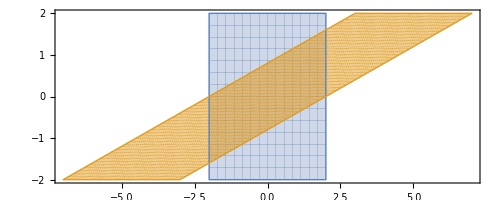

```mathematica
A=({{1, 2.5}, {0, 1}});
ParametricPlot[ {{x1,x2},A.{x1,x2}},{x1,-2,2},{x2,-2,2}]
```

##### Dilation

The matrix A=(r | 0
0 | r) is a dilation.  It stretches everything by r.  It has the simple formula
	x→A x = (r | 0
0 | r)x=r x

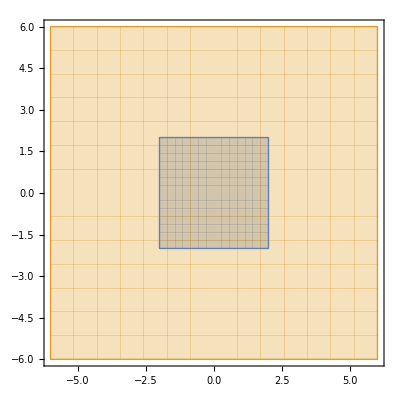

```mathematica
A=({{3, 0}, {0, 3}});
ParametricPlot[ {{x1,x2},A.{x1,x2}},{x1,-2,2},{x2,-2,2}]
```

##### Look at Table of pics on p78-80 of text.

### 1.10 Linear Models

#### Diets

Example 1. Our task is to work out how supply the Cambridge diet amounts with the ingredients.

-Graphics-

```mathematica
Aug={
{36,51,13,33},
{52,34,74, 45},
{0, 7, 1.1, 3}
};
RowReduce[Aug]//MatrixForm
```

(1 | 0. | 0. | 0.277223
0 | 1 | 0. | 0.391921
0 | 0 | 1 | 0.233231)

We need 27.7g of milk, 39.1g of soy and 23.3g of whey.

#### Resistor Circuits

Example 2. Our task is to work out the loop currents in the figure.

```mathematica
Aug={
{11, -3, 0, 30},
{-3,6, -1, 5},
{0, -1, 3, -25}};
MatrixForm[RowReduce[Aug]]
```

(1 | 0 | 0 | 3
0 | 1 | 0 | 1
0 | 0 | 1 | -8)

We need to know Ohm’s law and Kirchhoff’s voltage law.  

Ohm’s law v= R i  is just the definition of an R Ohm resistor. It relates the voltage drop v across the resistor to the current i through the resistor.  

Kirchhoff’s voltage law says “voltages sums to zero around a loop”.

#### Difference Equations

Take a look at the following exercise from our text.

### Projects

Take a look at the projects listed on the text book project page.  The bitly link expands to
https://media.pearsoncmg.com/aw/aw_lay_linearalg_6/project/lla06_projects.html